## Семинар по Wolfram Mathematica

### Определение переменных и функций.

Можно использовать просто знак равенства. Точка с запятой говорит, что не нужно выводить результат вычисления, который в случае определения есть правая часть определения. Чтобы  вычислить результат, нажмите shift+enter.

```mathematica
a=5
```

```mathematica
a=5;
```

```mathematica
a
```

Двоеточие равно (:=) тоже определяет переменные и функции, но другим образом. В случае знака = правая часть вычисляется в момент определения; в случае := правая часть вычисляется каждый раз при вызове функции. Мы положили а = 5, посмотрите на результат следующих вычислений.

```mathematica
b=a;
c:=a;
a=7;
```

```mathematica
b
```

```mathematica
c
```

Функции определяются следующим образом:

```mathematica
f[x_,y_]:=x+y+2;
f[5,1]
```

Обратите внимание на нижнее подчёркивание в аргументе. Оно необходимо, без него не заработает. У меня есть отдельный полуторачасовой семинар, рассказывающий про это подчёркивание, он будет лежать в extras. Пока просто примите, что функции определяются так и только так.

### Общие замечания по работе с Mathematica.

Все заранее определённые функции начинаются с большой буквы; если название состоит из нескольких букв, то заглавной является каждая первая буква нового слова. Sin, ArcSin, BesselJ. Натуральный логарифм - Log, а не Ln. Большинство названий интуитивно понятны.
В Mathematica встроена отличная документация. При наборе функций она подсказывает названия; справа от названия есть кпопка, открывающая справку по данной функции. Также справку можно получить, поставив курсор на функцию и нажав f1.
Для многих часто используемых функций и констант есть “красивое” написание. Функция Integrate - это то же самое, что ∫ - набирается <esc>int<esc>. Эта особенность математики делает возможным создание лекций прямо в ней. Я буду указывать написание красивых значков по мере их появления. Вообще, конечно, они гуглятся.
Справа можно заметить квадратные скобки. Они указывают структуру текста. Когда вы нажимаете shift+enter, вычисляется содержимое самой левой квадратной скобки, сколько бы инструкций в ней не было. Мы будем называть эти скобки блоками. Блоки бывают разных типов - этот блок текстовый, он не вычисляется совсем. Все типы блоков описаны в подменю style меню format.
Блоки в математике вычисляются. Не компилируется, не исполняются, не интерпретируются. Отличия между всеми этими словами сейчас разбирать бессмысленно, просто не удивляйтесь, когда я буду постоянно писать про вычисление функций.

### Интегрирование, дифференцирование, ряды.

Неопределённый интеграл. Можно написать как функцию с данными параметрами, так и красивое выражение, используя <esc>int<esc> для интеграла и <esc>dd<esc> для дифференциала.

```mathematica
Integrate[Sin[x],x]
```

```mathematica
∫Sin[x]ⅆx
```

Определённый интеграл. Нижний предел - ctrl+- (одновременно ctrl и -), из нижнего предела в верхий или обратно - ctrl+5, верхний предел - ctrl+6. Бесконечность <esc>inf<esc>. Тут даже набирать красивую версию быстрее, чем обычную.

```mathematica
Integrate[Exp[-x^2],{x,-Infinity,Infinity}]
```

```mathematica
∫_(-∞)^∞ ⅇ^(-x^2)ⅆx
```

Производные, в том числе и многократные. Корень - ctrl+2, знак частной производной <esc>pd<esc> (partial derivative, очевидно).

```mathematica
D[√x+y^3+ⅇ^-x,x]
```

```mathematica
D[√x y^3+ⅇ^-x,{x,2},y]
```

```mathematica
D[(√x y^3+ⅇ^-x), x,x,y]
```

Ряды. Знак суммы - <esc>sum<esc>, предел под суммой - ctrl+4 (не то же самое, что нижний предел интегрирования!), переход в верхний предел - ctrl+5, дробь - ctrl+/.

```mathematica
Sum[1/n^2,{n,1,Infinity}]
```

```mathematica
∑_(n=1)^∞ 1/n^2
```

### Построение графиков.

Надеюсь, тут всё очевидно. Стрелочки делаются - >, в этом месте они нужны по тем же причинам, что и нижнее подчёркивание в аргументах функций. В смысле, по причинам, неизвестным вам. Но они нужны.

```mathematica
Plot[x^2,{x,0,3},PlotStyle->{Green, Thick},AxesLabel->{"x","x^2"}]
```

Трёхмерный график. PlotRange задаёт интервал значений по вертикальной координате (там, где откладываются значения функций).

```mathematica
Plot3D[1/(x^2+y^2+1),{x,-3,3},{y,-3,3},PlotStyle->{Yellow},PlotRange-> {0,1.1},AxesLabel->{"x","y","f(x,y)"}]
```

Крайне полезно делать графики, зависящие от параметра. Manipulate вообще съедает всё, не только графики, но смотреть на меняющиеся графики полезнее всего.

```mathematica
Manipulate[Plot[1/((x-t)^2+1),{x,-3,3},PlotStyle->{Green, Thick},AxesLabel->{"x","f(x,t)"},PlotRange->{0,1.05},Filling->Bottom],{t,-5,5}]
```

То же в 3D, просто красоты ради.

```mathematica
Manipulate[Plot3D[1/((x-Sin[q])^2+(y-Cos[q])^2+1),{x,-3,3},{y,-3,3},PlotStyle->{Blue},PlotRange-> {0,1.1},AxesLabel->{"x","y","f(x,y,q)"}],{q,0,2Pi}]
```

### Решение уравнений

Обратите внимание на два знака равно. Кроме того, результат - не массив чисел, а массив подстановок. Мы сейчас не будем вдаваться вглубь; чтобы получить массив чисел, сделайте x /. Solve[... , x] (или с любой другой буквой кроме х).

```mathematica
Solve[x^8+x^4+1==0,x]
```

На тему численного решения есть несколько вариантов. FindRoot - это относительно надёжный, но он найдёт только один корень. Скорее всего, ближайший к той точке, которую вы укажете в фигурных скобочках рядом с переменной, относительно которой нужно решать.
Очевидно, мы не можем численно решать уравнение с буквенным параметром, поэтому нужно либо задавать конкретные значения параметрам, либо сразу их как-то использовать. Например, в графике. Это уравнение встречалось в первом семинаре.

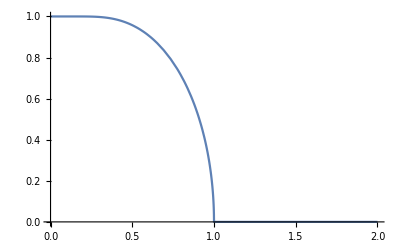

```mathematica
Plot[m/.FindRoot[m==Tanh[m/T],{m,1}],{T,0,2}]
```

Есть NSolve, который искренне попытается, но ничего не будет обещать.

```mathematica
NSolve[x^8+x^4+1==0,x]
```

```mathematica
NSolve[m==Tanh[2m],m]
```

### Численное интегрирование.

Асимптотики этого интеграла мы искали где-то в курсе.

```mathematica
Plot[{1/λ,NIntegrate[Exp[-λ t]/(1+t),{t,0,∞}]},{λ,1,10}]
```

Относительная ошибка показывает, правильно ли мы угадали первый порядок. Если да, то в числителе останется второй, а в знаменателе первый, так что отношение будет стремиться к нулю. Если ошиблись хотя бы на константу, первый порядок сверху выживет, а ошибка будет стремиться к некой константе.

```mathematica
Plot[(1/λ-NIntegrate[Exp[-λ t]/(1+t),{t,0,∞}])/(1/λ+NIntegrate[Exp[-λ t]/(1+t),{t,0,∞}]),{λ,1,50},PlotRange->{0,0.25}]
```

Относительная ошибка очень полезна, если просто график недостаточно нагляден.

```mathematica
Plot[{NIntegrate[Exp[-λ t]/(1+t),{t,0,∞}],Log[1/λ]},{λ,0,0.1},PlotRange->{0,10}]
```

```mathematica
Plot[(Log[1/λ]-NIntegrate[Exp[-λ t]/(1+t),{t,0,∞}])/(Log[1/λ]+NIntegrate[Exp[-λ t]/(1+t),{t,0,∞}]),{λ,0,0.1},PlotRange->{0,0.1}]
```

### Специальные функции.

Почти наверняка встроены в математику. Чаще всего, их название можно просто угадать: функция Бесселя, которая пишется J, функция Эйри, которая Ai...

```mathematica
BesselJ[0,0]
```

```mathematica
AiryAi[0]
```

```mathematica
Plot[BesselJ[1,t],{t,0,40}]
```

Если название не угадывается, гуглите.

### Диффуры.

Можно попросить решить аналитически.

```mathematica
DSolve[x''[t]+ω^2 x[t]==0,x[t],t]
```

В том числе с начальными условиями.

```mathematica
DSolve[{y''[x]+ω^2 y[x]==0,y[0]==1,y'[0]==0},y[x],x]
```

А можно вообще численно и с параметрами.

```mathematica
sol=ParametricNDSolve[{y''[x]+x^2*y'[x]+y[x]==a/(1+x^2),y[0]==1,y'[0]==0},y[x],{x,0,20},{a}];
```

```mathematica
Manipulate[Plot[y[x][a]/.sol,{x,0,20},PlotRange->All,PlotStyle->{Thick,Blue}],{a,0,2}]
```

### Линейная алгебра.

Перемножение матриц и векторов - точка. Потому что в английском dot product. Вектора не делятся на ко и контра, они все - просто массив чисел. Как ни забавно, это не мешает. Транспонирование - <esc>tr<esc>.

```mathematica
v1={1,2,3};
v2={1,2,3};
v1.v2
```

```mathematica
M1={{0,1,0},{0,0,1},{0,0,0}};
M1//MatrixForm
```

```mathematica
M1.M1//MatrixForm
```

```mathematica
M1 M1//MatrixForm
```

```mathematica
Eigensystem[M1+M1ᵀ]
```

{{-√2,√2,0},{{1,-√2,1},{1,√2,1},{-1,0,1}}}